## Time-dependent optimal control, Example 7.3

```mathematica
Clear["Global`*"];
```

Solve the Riccati equation:

```mathematica
Ssol1=NDSolveValue[{s'[t]== -1+2s[t]+s[t]^2,s[3]==0},s,{t,3,0}];
Ssol2=DSolveValue[{s'[t]== -1+2s[t]+s[t]^2,s[3]==0},s[t],t]//FullSimplify
```

1/(1-√2 Coth[√2 (-3+t)])

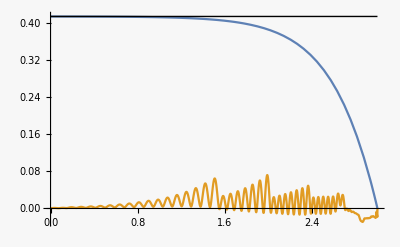

```mathematica
Plot[{Ssol2, 10^6(Ssol1[t]-Ssol2),√2-1},{t,0,3},PlotStyle->{,,{Thin,Black}}]
```

The numerical and analytic solutions agree!  Note, too, that although the solution “asymptotes” to √2-1, it has not quite reached this value at a time 3 before the end.

```mathematica
{Ssol2/.t->0,√2-1} //N
```

{0.414113,0.414214}